# Mathematica for Bioinformatics

by George I. Mias, PhD
["http://georgemias.org"](http://georgemias.org)

## Chapter 3: Statistics

## Descriptive Statistics

```mathematica
dataHeights={1.50,1.73,1.53,1.85,1.80,1.60,1.68,1.55,1.72,1.84}
```

{1.5,1.73,1.53,1.85,1.8,1.6,1.68,1.55,1.72,1.84}

```mathematica
Length[dataHeights]
```

10

```mathematica
Mean[dataHeights]
```

1.68

```mathematica
Median[dataHeights]
```

1.7

```mathematica
Variance[dataHeights]
```

0.0168

```mathematica
StandardDeviation[dataHeights]
```

0.129615

```mathematica
Max[dataHeights]
```

1.85

```mathematica
Min[dataHeights]
```

1.5

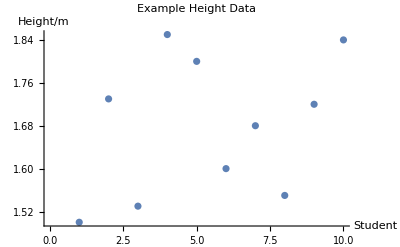

```mathematica
dataPlot=ListPlot[dataHeights,
PlotLabel-> "Example Height Data",
AxesLabel-> {"Student","Height/m"}]
```

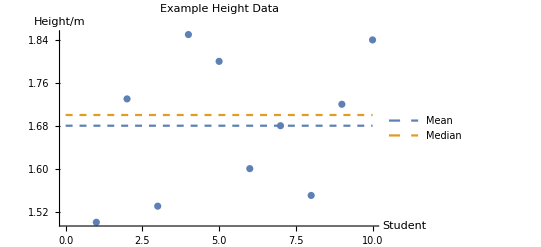

```mathematica
Show[dataPlot,
Plot[{Mean[dataHeights],Median[dataHeights]},
{x,0,10},
PlotStyle-> Dashed,
PlotLegends->{"Mean","Median"}]]
```

## A Short Probabilistic Sequence of Events

```mathematica
?RandomChoice
```

RandomChoice[{e_1,e_2,…}] gives a pseudorandom choice of one of the e_i. 
RandomChoice[list,n] gives a list of n pseudorandom choices. 
RandomChoice[list,{n_1,n_2,…}] gives an n_1×n_2×… array of pseudorandom choices. 
RandomChoice[{w_1,w_2,…}→{e_1,e_2,…}] gives a pseudorandom choice weighted by the w_i. 
RandomChoice[wlist→elist,n] gives a list of n weighted choices.
RandomChoice[wlist→elist,{n_1,n_2,…}] gives an n_1×n_2×… array of weighted choices.

```mathematica
randomFlips=RandomChoice[{"H","T"},1000];
```

```mathematica
Take[randomFlips,10]
```

{T,T,T,T,H,H,H,T,T,T}

```mathematica
Tally[randomFlips]
```

{{T,489},{H,511}}

```mathematica
talliesCoinFlip=SortBy[Tally[#],First]&/@RandomChoice[{"H","T"},{2000,1000}];
```

```mathematica
Dimensions[talliesCoinFlip]
```

{2000,2,2}

```mathematica
talliesCoinFlip[[1;;10]]
```

{{{H,500},{T,500}},{{H,485},{T,515}},{{H,492},{T,508}},{{H,489},{T,511}},{{H,472},{T,528}},{{H,503},{T,497}},{{H,481},{T,519}},{{H,508},{T,492}},{{H,521},{T,479}},{{H,488},{T,512}}}

```mathematica
N[Mean[talliesCoinFlip]]
```

{{H,500.059},{T,499.942}}

```mathematica
randomWord=StringJoin[RandomChoice[{"A","C","G","T"},100]]
```

ACCGTCAATTGAAGAAACCAGACCCGACCGAGACTACGCGCGCAAAAGCGACTCGTCTGCCCCAGACACAAGGGACCATCTCTTCGACTCGAAATCCCTC

```mathematica
randomWeightedSequence=StringJoin[RandomChoice[{0.29,0.21,0.21,0.29}-> {"A","C","G","T"},100]]
```

ATGGTTAGAGTTTCAGTGATTAATGCGCCCTCACGTCCTATACCTCTAACATTGAGTCCAACGTTGCAAGCTACAGAAACACTAAAATACTGAATATTAA

```mathematica
diceRoll=RandomInteger[{1,6},2]
```

{4,4}

```mathematica
diceRoll2=RandomChoice[Range[6],2]
```

{2,1}

```mathematica
exampleContinuous=RandomReal[1,1]
```

{0.971052}

## Examples of Discrete Distributions

### Bernoulli Distribution

```mathematica
?BernoulliDistribution
```

BernoulliDistribution[p] represents a Bernoulli distribution with probability parameter p.

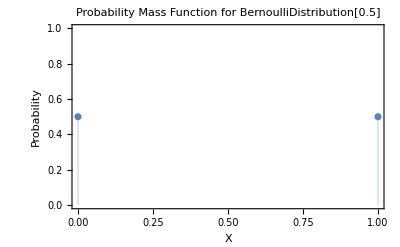

```mathematica
DiscretePlot[PDF[BernoulliDistribution[0.5],x],
{x,0,1},Frame->True,PlotLabel-> 
"Probability Mass Function for BernoulliDistribution[0.5]",
FrameLabel->{"X","Probability"}]
```

```mathematica
?CDF
```

CDF[dist,x] gives the cumulative distribution function for the symbolic distribution dist evaluated at x.
CDF[dist,{x_1,x_2,…}] gives the multivariate cumulative distribution function for the symbolic distribution dist evaluated at {x_1,x_2,…}.
CDF[dist] gives the CDF as a pure function.

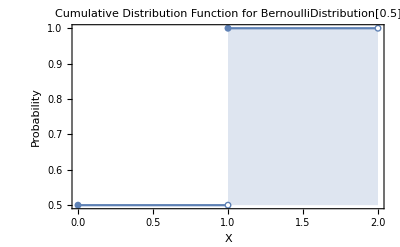

```mathematica
DiscretePlot[CDF[BernoulliDistribution[0.5],x],
{x,0,1}, ExtentSize->Right,
ExtentMarkers->{"Filled","Empty"},
Frame-> True,
PlotLabel->
 "Cumulative Distribution Function for
 BernoulliDistribution[0.5]",
FrameLabel->{"X","Probability"}]
```

```mathematica
PDF[BernoulliDistribution[0.5],x]
```

Piecewise[{{0.5, x==0||x==1}, {0, True}}]

```mathematica
CDF[BernoulliDistribution[0.5],x]
```

Piecewise[{{0, x<0}, {0.5, 0≤x<1}, {1, True}}]

```mathematica
PDF[BernoulliDistribution[p],x]
```

Piecewise[{{1-p, x==0}, {p, x==1}, {0, True}}]

```mathematica
CDF[BernoulliDistribution[p],x]
```

Piecewise[{{0, x<0}, {1-p, 0≤x<1}, {1, True}}]

```mathematica
RandomVariate[BernoulliDistribution[0.5],10]
```

{0,1,0,1,0,1,1,1,1,1}

### Binomial Distribution

```mathematica
?BinomialDistribution
```

BinomialDistribution[n,p] represents a binomial distribution with n trials and success probability p.

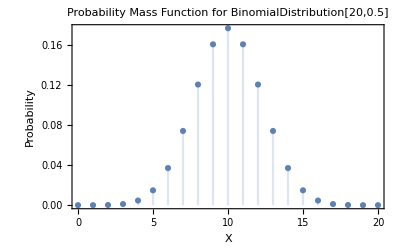

```mathematica
DiscretePlot[PDF[BinomialDistribution[20,0.5],x],
{x,0,20},Frame->True,
PlotLabel-> 
"Probability Mass Function 
for BinomialDistribution[20,0.5]",
FrameLabel->{"X","Probability"}]
```

```mathematica
PDF[BinomialDistribution[20,0.5],5]
```

0.0147858

```mathematica
Table[PDF[BinomialDistribution[20,0.5],x],{x,0,20}]
```

{9.53674×10^-7,0.0000190735,0.000181198,0.00108719,0.00462055,0.0147858,0.0369644,0.0739288,0.120134,0.160179,0.176197,0.160179,0.120134,0.0739288,0.0369644,0.0147858,0.00462055,0.00108719,0.000181198,0.0000190735,9.53674×10^-7}

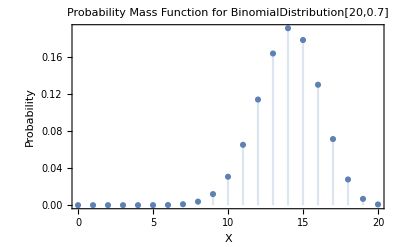

```mathematica
DiscretePlot[PDF[BinomialDistribution[20,0.7],x],
{x,0,20},Frame->True,PlotLabel->
 "Probability Mass Function 
for BinomialDistribution[20,0.7]",
FrameLabel->{"X","Probability"}]
```

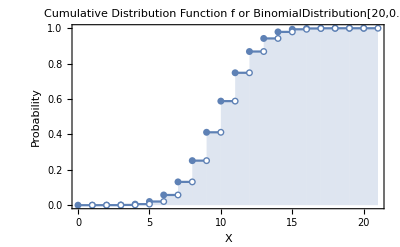

```mathematica
DiscretePlot[CDF[BinomialDistribution[20,0.5],x],
{x,0,20}, ExtentSize->Right,
ExtentMarkers->{"Filled","Empty"},Frame-> True,
PlotLabel->
 "Cumulative Distribution Function f
or BinomialDistribution[20,0.5]",
FrameLabel->{"X","Probability"}]
```

```mathematica
PDF[BinomialDistribution[n,p],x]
```

Piecewise[{{(1-p)^(n-x) p^x Binomial[n,x], 0≤x≤n}, {0, True}}]

```mathematica
CDF[BinomialDistribution[n,p],x]
```

Piecewise[{{BetaRegularized[1-p,n-Floor[x],1+Floor[x]], 0≤x<n}, {1, x≥n}, {0, True}}]

```mathematica
Mean[BinomialDistribution[n,p]]
```

n p

```mathematica
Variance[BinomialDistribution[n,p]]
```

n (1-p) p

```mathematica
RandomVariate[BinomialDistribution[20,0.25],10]
```

{6,5,3,6,3,7,1,5,4,4}

### Geometric Distribution

```mathematica
PDF[GeometricDistribution[p],x]
```

Piecewise[{{(1-p)^x p, x≥0}, {0, True}}]

```mathematica
?GeometricDistribution
```

GeometricDistribution[p] represents a geometric distribution with probability parameter p.

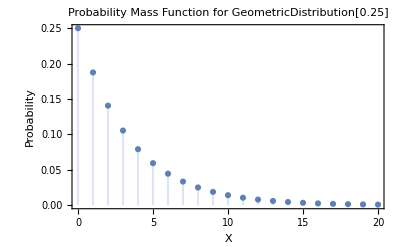

```mathematica
DiscretePlot[PDF[GeometricDistribution[0.25],x],
{x,0,20},Frame->True,
PlotLabel-> "Probability Mass Function 
for GeometricDistribution[0.25]",
FrameLabel->{"X","Probability"}]
```

```mathematica
PDF[GeometricDistribution[0.25],3]
```

0.105469

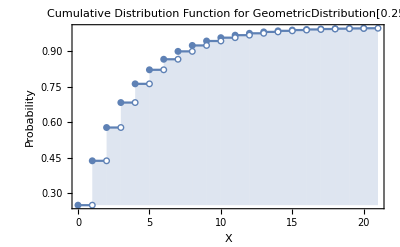

```mathematica
DiscretePlot[CDF[GeometricDistribution[0.25],x],
{x,0,20}, ExtentSize->Right,
ExtentMarkers->{"Filled","Empty"},Frame-> True,
PlotLabel-> 
"Cumulative Distribution Function
 for GeometricDistribution[0.25]",
FrameLabel->{"X","Probability"}]
```

```mathematica
Table[Sum[PDF[GeometricDistribution[0.25],x],{x,0,i}],{i,1,21}]
```

{0.4375,0.578125,0.683594,0.762695,0.822021,0.866516,0.899887,0.924915,0.943686,0.957765,0.968324,0.976243,0.982182,0.986637,0.989977,0.992483,0.994362,0.995772,0.996829,0.997622,0.998216}

```mathematica
CDF[GeometricDistribution[p],x]
```

Piecewise[{{1-(1-p)^(1+Floor[x]), x≥0}, {0, True}}]

### Poisson Distribution

```mathematica
PDF[PoissonDistribution[λ],x]
```

Piecewise[{{(ⅇ^-λ λ^x)/(x!), x≥0}, {0, True}}]

```mathematica
Mean[PoissonDistribution[λ]]
```

λ

```mathematica
Variance[PoissonDistribution[λ]]
```

λ

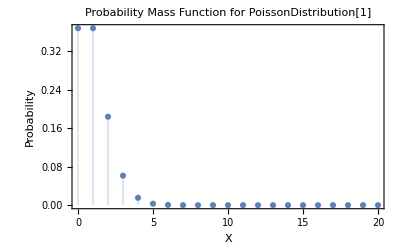

```mathematica
DiscretePlot[PDF[PoissonDistribution[1],x],
{x,0,20},Frame->True,
PlotLabel->
 "Probability Mass Function
 for PoissonDistribution[1]",
FrameLabel->{"X","Probability"},
PlotRange->Full]
```

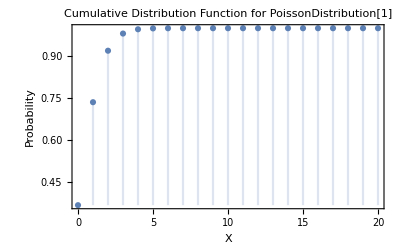

```mathematica
DiscretePlot[CDF[PoissonDistribution[1],x],
{x,0,20},Frame->True,
PlotLabel->
 "Cumulative Distribution Function
 for PoissonDistribution[1]",
FrameLabel->{"X","Probability"},
PlotRange-> Full]
```

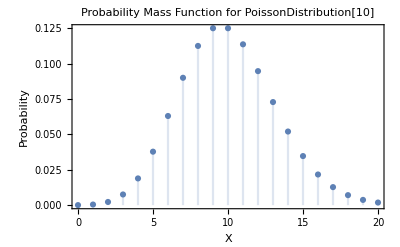

```mathematica
DiscretePlot[PDF[PoissonDistribution[10],x],
{x,0,20},Frame->True,
PlotLabel-> "Probability Mass Function
 for PoissonDistribution[10]",
FrameLabel->{"X","Probability"}]
```

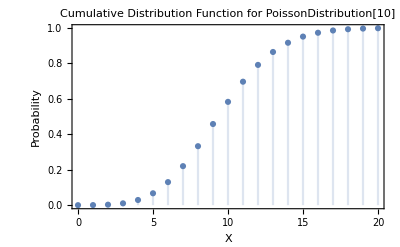

```mathematica
DiscretePlot[CDF[PoissonDistribution[10],x],
{x,0,20},Frame->True,
PlotLabel->
 "Cumulative Distribution Function for
 PoissonDistribution[10]",
FrameLabel->{"X","Probability"}]
```

### Hypergeometric Distribution

```mathematica
?HypergeometricDistribution
```

HypergeometricDistribution[n,n_succ,n_tot] represents a hypergeometric distribution.

```mathematica
Mean[HypergeometricDistribution[n,Subscript[n, succ],Subscript[n, tot]]]
```

(n n_succ)/n_tot

```mathematica
PDF[HypergeometricDistribution[Subscript[n, group],Subscript[M, T],N],i]
```

Piecewise[{{(Binomial[N-M_T,-i+n_group] Binomial[M_T,i])/Binomial[N,n_group], 0≤i≤M_T&&-N+M_T+n_group≤i≤M_T&&0≤i≤n_group&&-N+M_T+n_group≤i≤n_group}, {0, True}}]

```mathematica
Table[N[PDF[HypergeometricDistribution[10,5,100],i]],{i,1,5}]
```

{0.339391,0.0702188,0.00638353,0.000251038,3.34717×10^-6}

```mathematica
genesUpregulated ={"TAB1","TNFSF13B","MALT1","TIRAP","CHUK","TNFRSF13C","PARP1","CSNK2A1","IKBA","CSNK2B","LTBR","LYN","MYD88","GADD45B","ATM","NFKB1","NFKB2","NFKBIA","AKT3","PIAS4","FOS","JUN"};
```

```mathematica
Needs["MathIOmica`"]
```

MathIOmica (http://mathiomica.org), by [G. Mias Lab](http://georgemias.org).

```mathematica
exampleORA=GOAnalysis[genesUpregulated];
```

```mathematica
exampleORA[[1;;3]]
```

<|GO:0038095→{{6.75904×10^-14,3.56877×10^-11,True},{20,251,47250,8},{{Fc-epsilon receptor signaling pathway,biological_process},{{TAB1},{MALT1},{CHUK},{LYN},{NFKB1},{NFKBIA},{FOS},{JUN}}}},GO:0005515→{{2.19898×10^-13,4.69303×10^-11,True},{20,8801,47250,19},{{protein binding,molecular_function},{{TAB1},{TNFSF13B},{MALT1},{TIRAP},{CHUK},{PARP1},{CSNK2A1},{CSNK2B},{LTBR},{LYN},{GADD45B},{ATM},{NFKB1},{NFKB2},{NFKBIA},{AKT3},{PIAS4},{FOS},{JUN}}}},GO:0051092→{{2.6665×10^-13,4.69303×10^-11,True},{20,155,47250,7},{{positive regulation of NF-kappaB transcription factor activity,biological_process},{{TAB1},{MALT1},{TIRAP},{CHUK},{NFKB1},{NFKB2},{NFKBIA}}}}|>

## Examples of Continuous Distributions

### Uniform Distribution

```mathematica
PDF[UniformDistribution[{a,b}],x]
```

Piecewise[{{1/(-a+b), a≤x≤b}, {0, True}}]

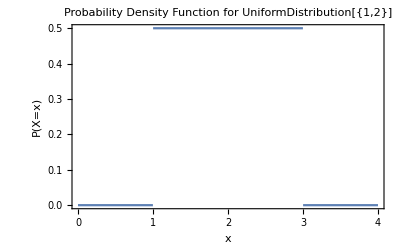

```mathematica
Plot[PDF[UniformDistribution[{1,3}],x],
{x,0,4},PlotRange-> All,Frame-> True,
FrameLabel-> {"x","P(X=x)"},
PlotLabel->"Probability Density Function
 for UniformDistribution[{1,2}]"]
```

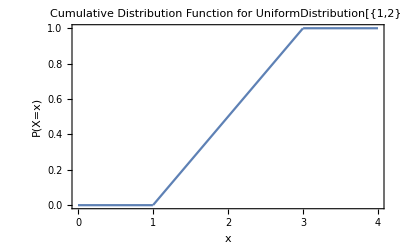

```mathematica
Plot[CDF[UniformDistribution[{1,3}],x],
{x,0,4},PlotRange-> All,Frame-> True,
FrameLabel-> {"x","P(X=x)"},
PlotLabel->"Cumulative Distribution Function
 for UniformDistribution[{1,2}]"]
```

```mathematica
Integrate[PDF[UniformDistribution[{1,3}],x],{x,-Infinity,Infinity}]
```

1

```mathematica
D[CDF[UniformDistribution[{1,3}],x],x]
```

Piecewise[{{0, x<1}, {1/2, 1<x<3}, {0, x>3}, {Indeterminate, True}}]

```mathematica
Mean[UniformDistribution[{a,b}]]
```

(a+b)/2

```mathematica
Variance[UniformDistribution[{a,b}]]
```

1/12 (-a+b)^2

```mathematica
PDF[UniformDistribution[{{Subscript[x, min],Subscript[x, max]},{Subscript[y, min],Subscript[y, max]},{Subscript[z, min],Subscript[z, max]}}],{x,y,z}]
```

Piecewise[{{1/((x_max-x_min) (y_max-y_min) (z_max-z_min)), x-x_min≥0&&y-y_min≥0&&z-z_min≥0&&-x+x_max≥0&&-y+y_max≥0&&-z+z_max≥0}, {0, True}}]

```mathematica
PDF[UniformDistribution[{{1,3},{1,4},{0,2}}],{x,y,z}]
```

Piecewise[{{1/12, -1+x≥0&&-1+y≥0&&z≥0&&3-x≥0&&4-y≥0&&2-z≥0}, {0, True}}]

```mathematica
Integrate[PDF[UniformDistribution[{{1,3},{1,4},{0,2}}],{x,y,z}],{x,-Infinity,Infinity},{y,-Infinity,Infinity}]
```

Piecewise[{{1/2, 0≤z≤2}, {0, True}}]

### Exponential Distribution

```mathematica
?ExponentialDistribution
```

ExponentialDistribution[λ] represents an exponential distribution with scale inversely proportional to parameter λ.

```mathematica
PDF[ExponentialDistribution[λ],x]
```

Piecewise[{{ⅇ^(-x λ) λ, x≥0}, {0, True}}]

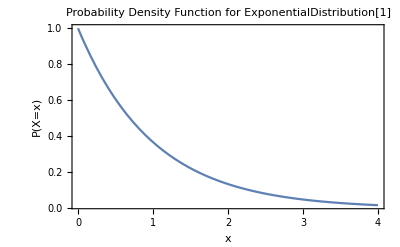

```mathematica
Plot[PDF[ExponentialDistribution[1],x],
{x,0,4},PlotRange-> All,Frame-> True,
FrameLabel-> {"x","P(X=x)"},
PlotLabel->"Probability Density Function
 for ExponentialDistribution[1]"]
```

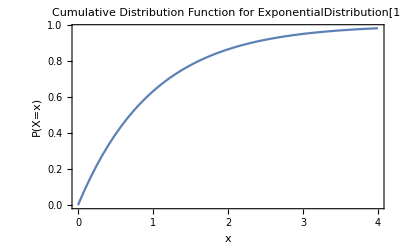

```mathematica
Plot[CDF[ExponentialDistribution[1],x],
{x,0,4},PlotRange-> All,Frame-> True,
FrameLabel-> {"x","P(X=x)"},
PlotLabel->"Cumulative Distribution Function
 for ExponentialDistribution[1]"]
```

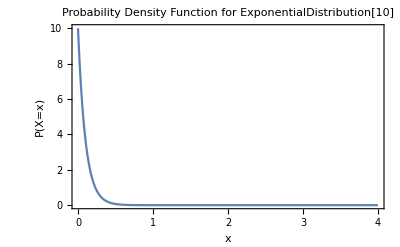

```mathematica
Plot[PDF[ExponentialDistribution[10],x],
{x,0,4},PlotRange-> All,Frame-> True,
FrameLabel-> {"x","P(X=x)"},
PlotLabel->"Probability Density Function
 for ExponentialDistribution[10]"]
```

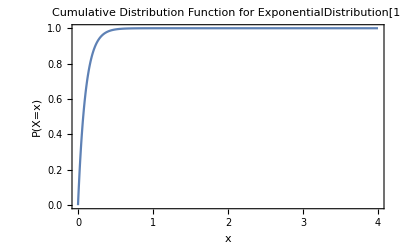

```mathematica
Plot[CDF[ExponentialDistribution[10],x],
{x,0,4},PlotRange-> All,Frame-> True,
FrameLabel-> {"x","P(X=x)"},
PlotLabel->"Cumulative Distribution Function
 for ExponentialDistribution[1]"]
```

```mathematica
Mean[ExponentialDistribution[λ]]
```

1/λ

```mathematica
Variance[ExponentialDistribution[λ]]
```

1/λ^2

### Normal Distribution

```mathematica
PDF[NormalDistribution[μ,σ],x]
```

(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)

```mathematica
Integrate[PDF[NormalDistribution[μ,σ],x],{x,-Infinity,Infinity},Assumptions->σ≥ 0 ]
```

1

```mathematica
Integrate[PDF[NormalDistribution[μ,σ],x],{x,-Infinity,Infinity} ]
```

ConditionalExpression[1/(√(1/σ^2) σ),Re[σ^2]≥0]

```mathematica
CDF[NormalDistribution[μ,σ],x]
```

1/2 Erfc[(-x+μ)/(√2 σ)]

```mathematica
Table[N[CDF[NormalDistribution[1,1],x]],{x,0,5,0.5}]
```

{0.158655,0.308538,0.5,0.691462,0.841345,0.933193,0.97725,0.99379,0.99865,0.999767,0.999968}

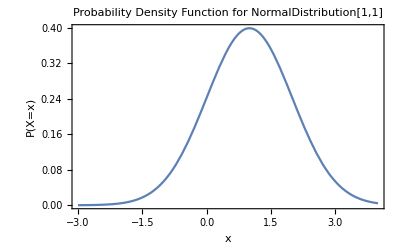

```mathematica
Plot[PDF[NormalDistribution[1,1],x],{x,-3,4},PlotRange-> All,Frame-> True,
FrameLabel-> {"x","P(X=x)"},PlotLabel-> "Probability Density Function for NormalDistribution[1,1]"]
```

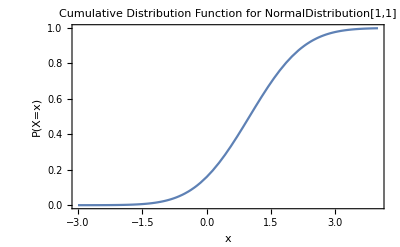

```mathematica
Plot[CDF[NormalDistribution[1,1],x],
{x,-3,4},PlotRange-> All,Frame-> True,
FrameLabel-> {"x","P(X=x)"},PlotLabel->"Cumulative Distribution Function for NormalDistribution[1,1]"]
```

```mathematica
Mean[NormalDistribution[μ,σ]]
```

μ

```mathematica
Variance[NormalDistribution[μ,σ]]
```

σ^2

```mathematica
sampleNormal=RandomVariate[NormalDistribution[0,1],1000];
```

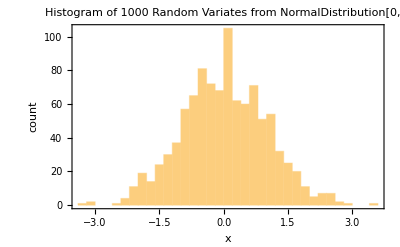

```mathematica
Histogram[sampleNormal,Frame-> True,
FrameLabel->{"x","count"},
PlotLabel->"Histogram of 1000 Random Variates
 from NormalDistribution[0,1]"]
```

```mathematica
Quantile[NormalDistribution[0,1],0.95]
```

1.64485

```mathematica
Quantile[NormalDistribution[0,1],{0.25,0.75}]
```

{-0.67449,0.67449}

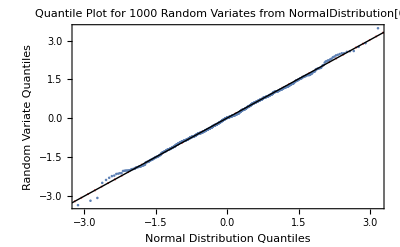

```mathematica
QuantilePlot[sampleNormal,
ReferenceLineStyle->Red,
FrameLabel->{"Normal Distribution Quantiles",
"Random Variate Quantiles"},
PlotLabel->"Quantile Plot for 1000 Random Variates
from NormalDistribution[0,1]"]
```

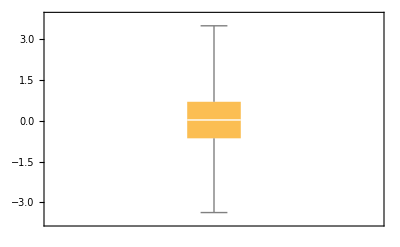

```mathematica
BoxWhiskerChart[sampleNormal]
```

```mathematica
sampleNormal2=RandomVariate[NormalDistribution[1.5,1],1000];
```

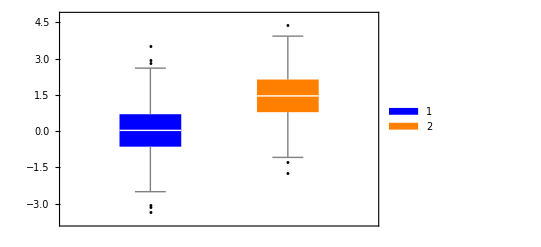

```mathematica
BoxWhiskerChart[{sampleNormal,sampleNormal2},
"Outliers",ChartLegends->{"1","2"},
ChartStyle->{Blue,Orange}]
```

### Chi-Squared distribution

```mathematica
PDF[ChiSquareDistribution[ν],x]
```

Piecewise[{{(2^(-ν/2) ⅇ^(-x/2) x^(-1+ν/2))/Gamma[ν/2], x>0}, {0, True}}]

```mathematica
CDF[ChiSquareDistribution[ν],x]
```

Piecewise[{{GammaRegularized[ν/2,0,x/2], x>0}, {0, True}}]

### F-ratio distribution

```mathematica
PDF[FRatioDistribution[n,m],x]
```

Piecewise[{{(m^(m/2) n^(n/2) x^(-1+n/2) (m+n x)^(1/2 (-m-n)))/Beta[n/2,m/2], x>0}, {0, True}}]

```mathematica
CDF[FRatioDistribution[n,m],x]
```

Piecewise[{{BetaRegularized[(n x)/(m+n x),n/2,m/2], x>0}, {0, True}}]

### Student-t Distribution

```mathematica
PDF[StudentTDistribution[ν],x]
```

((ν/(x^2+ν))^((1+ν)/2))/(√ν Beta[ν/2,1/2])

```mathematica
CDF[StudentTDistribution[ν],x]
```

Piecewise[{{1/2 BetaRegularized[ν/(x^2+ν),ν/2,1/2], x≤0}, {1/2 (1+BetaRegularized[x^2/(x^2+ν),1/2,ν/2]), True}}]

```mathematica
Variance[StudentTDistribution[ν]]
```

Piecewise[{{ν/(-2+ν), ν>2}, {Indeterminate, True}}]

```mathematica
Mean[StudentTDistribution[ν]]
```

Piecewise[{{0, ν>1}, {Indeterminate, True}}]

## Other Distributions

Statistical Distributions

WolframAlphaQueryResults

```mathematica
?MultinormalDistribution
```

MultinormalDistribution[μ,Σ] represents a multivariate normal (Gaussian) distribution with mean vector μ and covariance matrix Σ.
MultinormalDistribution[Σ] represents a multivariate normal distribution with zero mean and covariance matrix Σ.

```mathematica
?MultinomialDistribution
```

MultinomialDistribution[n,{p_1,p_2,…,p_m}] represents a multinomial distribution with n trials and probabilities p_i.

## Data Sets

### ExampleData

```mathematica
ExampleData[]
```

{AerialImage,Audio,ColorTexture,Dataset,Geometry3D,LinearProgramming,MachineLearning,Matrix,NetworkGraph,Sound,Statistics,TestAnimation,TestImage,TestImage3D,TestImageSet,Text,Texture}

```mathematica
exampleDataStatistics=ExampleData["Statistics"];
```

```mathematica
Length[exampleDataStatistics]
```

111

```mathematica
exampleDataStatistics[[1;;10]]
```

{{Statistics,AirlinePassengerMiles},{Statistics,AirplaneGlass},{Statistics,AnimalWeights},{Statistics,AnorexiaTreatment},{Statistics,AnscombeRegressionLines},{Statistics,AustraliaAIDS},{Statistics,AustraliaRainfall},{Statistics,Baboon},{Statistics,BatchChemicalProcessYields},{Statistics,BeaverBodyTemperatures}}

```mathematica
ExampleData[{"Statistics","DenmarkMelanoma"},"Properties"]
```

{ApplicationAreas,ColumnDescriptions,ColumnHeadings,ColumnTypes,DataElements,DataType,Description,Dimensions,EventData,EventSeries,LongDescription,Name,ObservationCount,Source,TimeSeries}

```mathematica
ExampleData[{"Statistics","DenmarkMelanoma"},"Description"]
```

Survival from malignant melanoma.

```mathematica
ExampleData[{"Statistics","DenmarkMelanoma"},"Source"]
```

P. K. Andersen, O. Borgan, R. D. Gill and N. Keiding (1993) Statistical Models based on Counting Processes. Springer.

```mathematica
ExampleData[{"Statistics","BoneMarrowTransplants"},"Description"]
```

Autologous and allogeneic bone marrow transplants

```mathematica
ExampleData[{"Statistics","BoneMarrowTransplants"},"ApplicationAreas"]
```

Medicine

```mathematica
ExampleData[{"Statistics","BoneMarrowTransplants"},"LongDescription"]
```

A sample of 101 patients with advanced acute myelogenous leukemia reported to the International Bone Marrow Transplant Registry. Fifty-one of these patients had received an autologous (auto) bone marrow transplant in which, after high doses of chemotherapy, their own marrow was reinfused to replace their destroyed immune system. Fifty patients had an allogeneic (allo) bone marrow transplant where marrow from an HLA-matched sibling was used to replenish their immune systems. These data are right censored.

```mathematica
ExampleData[{"Statistics","BoneMarrowTransplants"},"Source"]
```

Klein and Moeschberger (1997) Survival Analysis Techniques for Censored and truncated data,Springer.

```mathematica
ExampleData[{"Statistics","BoneMarrowTransplants"},"Dimensions"]
```

{101,3}

```mathematica
dataBoneMarrow=ExampleData[{"Statistics","BoneMarrowTransplants"},"DataElements"];
```

```mathematica
dataBoneMarrow//Short
```

{{0.03,1,0},«99»,{56.086,2,0}}

```mathematica
?Postfix
```

Postfix[f[expr]] prints with f[expr] given in default postfix form: expr//f. 
Postfix[f[expr],h] prints as exprh.

```mathematica
ExampleData[{"Statistics","BoneMarrowTransplants"},"ColumnTypes"]
```

{Numeric,Numeric,Numeric}

```mathematica
ExampleData[{"Statistics","BoneMarrowTransplants"},#]&@"ColumnDescriptions"
```

{Time to death or relapse in months,Type of transplant (1 = allogeneic, 2 = autologous),Leukemia-free survival indicator (1 = alive without relapse, 0 = dead or relapse)}

```mathematica
?Gather
```

Gather[list] gathers the elements of list into sublists of identical elements.
Gather[list,test] applies test to pairs of elements to determine if they should be considered identical.

```mathematica
dataBoneMarrowSeparated=Gather[dataBoneMarrow, #1[[2]]==#2[[2]]&];
```

```mathematica
dataBoneMarrowSeparated//Short
```

{{{0.03,1,0},«48»,{60.625,1,1}},{«1»}}

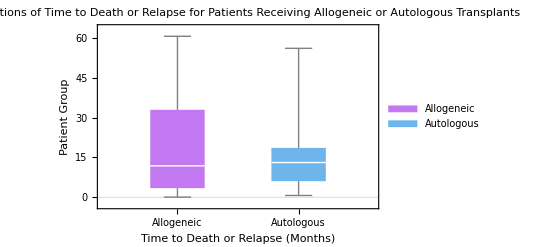

```mathematica
BoxWhiskerChart[{dataBoneMarrowSeparated[[1,All,1]],
dataBoneMarrowSeparated[[2,All,1]]},
PlotTheme-> "Scientific",ChartStyle->"Pastel",
FrameLabel->{ "Time to Death or Relapse (Months)",
"Patient Group"},PlotLabel->
"Distributions of Time to Death or Relapse for 
 Patients Receiving Allogeneic or Autologous Transplants",
ChartLabels->{"Allogeneic","Autologous"},
ChartLegends->{"Allogeneic","Autologous"}]
```

```mathematica
Mean[N[#]]&/@{dataBoneMarrowSeparated[[1,All,1]],dataBoneMarrowSeparated[[2,All,1]]}
```

{18.5519,16.7317}

```mathematica
StandardDeviation[N[#]]&/@{dataBoneMarrowSeparated[[1,All,1]],dataBoneMarrowSeparated[[2,All,1]]}
```

{17.7627,13.9388}

```mathematica
dataBoneMarrowSeparatedAliveDead=Gather[dataBoneMarrow, #1[[2]]==#2[[2]]&&#1[[3]]==#2[[3]]&];
```

```mathematica
dataBoneMarrowSeparatedAliveDead[[1]]//Short
```

{{0.03,1,0},{0.493,1,0},«19»,{20.066,1,0}}

```mathematica
dataBoneMarrowSeparatedAliveDead[[2]]//Short
```

{{4.441,1,1},«26»,{60.625,1,1}}

```mathematica
dataBoneMarrowSeparatedAliveDead[[3]]//Short
```

{{0.658,2,0},«26»,{56.086,2,0}}

```mathematica
dataBoneMarrowSeparatedAliveDead[[4]]//Short
```

{{4.836,2,1},«21»,{48.322,2,1}}

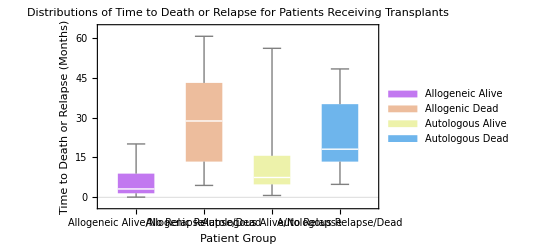

```mathematica
BoxWhiskerChart[
dataBoneMarrowSeparatedAliveDead[[All,All,1]],
PlotTheme-> "Scientific",ChartStyle->"Pastel",
FrameLabel->{ "Patient Group",
"Time to Death or Relapse (Months)"},PlotLabel->
"Distributions of Time to Death or Relapse for 
 Patients Receiving Transplants",
ChartLabels->{"Allogeneic\n Alive/No Relapse",
"Allogenic\n Relapse/Dead",
"Autologous\n Alive/No Relapse",
"Autologous\n Relapse/Dead"},
ChartLegends->{"Allogeneic Alive","Allogenic Dead",
"Autologous Alive","Autologous Dead"}]
```

```mathematica
Options[SmoothHistogram]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→Automatic,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

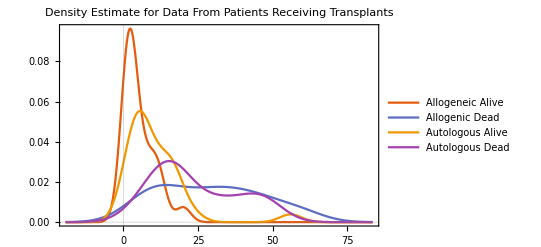

```mathematica
SmoothHistogram[
dataBoneMarrowSeparatedAliveDead[[All,All,1]],
PlotTheme->"Scientific",
PlotLabel->"Density Estimate for Data From
 Patients Receiving Transplants",
PlotLegends->{"Allogeneic Alive","Allogenic Dead",
"Autologous Alive","Autologous Dead"}]
```

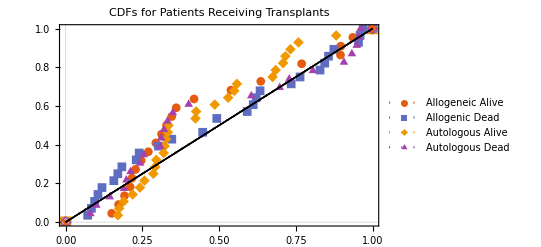

```mathematica
ProbabilityPlot[
dataBoneMarrowSeparatedAliveDead[[All,All,1]],
PlotTheme->"Scientific",PlotLabel->
"CDFs for \n Patients Receiving Transplants",
PlotLegends->{"Allogeneic Alive","Allogenic Dead",
"Autologous Alive","Autologous Dead"},
PlotMarkers->Automatic]
```

### ResourceData

```mathematica
?ResourceData
```

ResourceData[resource] gives the primary content of the specified resource.
ResourceData[resource,elem] gives element elem of the content of the resource.

```mathematica
ResourceSearch["Cancer"]
```

{ResourceObject[…],ResourceObject[…]}

```mathematica
roLeukemiaBoneMarrow=ResourceData["Sample Data: Esophageal Cancer"]
```

Dataset[<>]

### Entity Types

```mathematica
entityValues=EntityValue[];
```

```mathematica
entityValues[[1;;10]]
```

{AdministrativeDivision,Aircraft,Airline,Airport,Alphabet,AmusementPark,AmusementParkRide,AnatomicalFunctionalConcept,AnatomicalStructure,Artwork}

```mathematica
proteinList=EntityList["Protein"];
```

```mathematica
Length[proteinList]
```

27479

```mathematica
proteinList[[1;;10]]
```

{alpha 1B-glycoprotein precursor,DEK oncogene,translocase of inner mitochondrial membrane 23 (yeast) homolog,allograft inflammatory factor 1 isoform 1,allograft inflammatory factor 1 isoform 3,absent in melanoma 1,adenylate kinase 1,adenylate kinase 2 isoform a,aminoacylase 1,ATP-binding cassette, sub-family A, member 2 isoform b}

```mathematica
diseaseList=EntityList["Disease"];
```

```mathematica
Length[diseaseList]
```

10886

```mathematica
diseaseList[[1;;10]]
```

{Asthma,CerebrovascularDisease,IschemicHeartDisease,salmonella infections,unclassified salmonella infections,unspecified type of salmonella infection,shigellosis,unclassified specified shigella infections,bacterial food poisoning,unspecified type of bacterial food poisoning}

```mathematica
Entity["Disease","ICDNine205.0"]
```

acute myeloid leukemia

```mathematica
amlEntity=Entity["Disease","ICDNine205.0"]
```

acute myeloid leukemia

```mathematica
InputForm[amlEntity]
```

Entity["Disease", "ICDNine205.0"]

```mathematica
amlEntity["Properties"]
```

{average patient age,average patient BMI,average temperature,average diastolic blood pressure,average patient height,ICD-9 code,ICD-10 code,name,average systolic blood pressure,average patient weight}

```mathematica
InputForm[#]&/@amlEntity["Properties"]
```

{EntityProperty["Disease", "AgeMean"],EntityProperty["Disease", "BodyMassIndexMean"],EntityProperty["Disease", "BodyTemperatureMean"],EntityProperty["Disease", "DiastolicMean"],EntityProperty["Disease", "HeightMean"],EntityProperty["Disease", "ICDNineCode"],EntityProperty["Disease", "ICDTenCode"],EntityProperty["Disease", "Name"],EntityProperty["Disease", "SystolicMean"],EntityProperty["Disease", "WeightMean"]}

```mathematica
amlEntity["AgeMean"]
```

53.1106 yr

```mathematica
amlEntity["ICDTenCode"]
```

ICD-10 C92.0

### Example: The Golub ALL AML Data Set

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
golubAssociation=<<"golubAssociation";
```

```mathematica
golubAssociation//Short
```

<|AML→<|AFFX-BioDn-3_at→{«1»},«3570»|>,ALL→«1»|>

```mathematica
hu6800IDtoAnnotation=<<"hu6800IDtoAnnotation";
```

```mathematica
hu6800IDtoAnnotation[[1;;4]]
```

<|Probe Set ID→{Gene Symbol,Gene Title,Entrez Gene ID,Cytoband},AB000409_at→{MKNK1,MAP kinase interacting serine/threonine kinase 1,8569,1p33},AB000410_s_at→{OGG1,8-oxoguanine DNA glycosylase,4968,3p26.2},AB000450_at→{VRK2,vaccinia related kinase 2,7444,2p16.1}|>

```mathematica
hu6800IDtoAnnotation["M71243_f_at"]
```

{GYPA,glycophorin A (MNS blood group),2993,4q31.21}

```mathematica
Query[Select[Or@@StringContainsQ[#,"myosin light chain 6B",IgnoreCase->False]&]]@hu6800IDtoAnnotation
```

<|M31211_s_at→{MYL6B,myosin light chain 6B,140465,12q13.13}|>

```mathematica
hu6800IDtoAnnotation["M31211_s_at"]
```

{MYL6B,myosin light chain 6B,140465,12q13.13}

```mathematica
?StringMatchQ
```

StringMatchQ[string,patt] tests whether "string" matches the string pattern patt. 
StringMatchQ[string,RegularExpression[regex]] tests whether "string" matches the specified regular expression. 
StringMatchQ[{s_1,s_2,…},p] gives the list of results for each of the s_i. 
StringMatchQ[patt] represents an operator form of StringMatchQ that can be applied to an expression.

```mathematica
myosinExample=Query[All,"M31211_s_at"]@golubAssociation
```

<|AML→{-0.929698,-1.21439,-1.36559,-1.03054,-1.29915,-0.401122,-0.263245,-1.27241,-0.651176,-0.323125,-1.43473,-0.203518,-1.04336,-1.22702,-1.28071,0.260207,-1.05801,-0.720331,-0.809905,-0.588208,-0.513632,-0.247296,-1.42036,-1.48163,-1.3111},ALL→{0.21673,-0.0512012,0.0512196,0.0658298,0.355842,-0.0764156,-0.298932,-0.46567,0.490372,0.651373,0.715212,0.148149,0.354363,-0.466193,0.576175,0.417461,-0.407586,0.388138,0.266817,0.634913,0.707898,-0.775871,0.0765331,0.108658,0.224704,0.466898,-0.87136,0.193097,-0.37865,-0.0896119,0.284866,0.51995,-0.204948,0.560927,-0.0758743,0.726773,0.337038,0.374954,0.146782,-0.474574,0.170777,0.136991,0.107438,-0.55069,0.279121,-0.665758,0.545882}|>

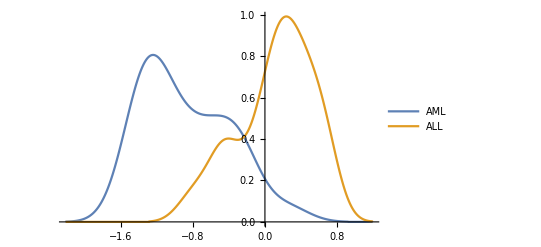

```mathematica
SmoothHistogram[myosinExample]
```

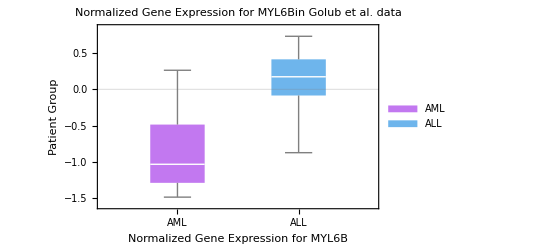

```mathematica
BoxWhiskerChart[myosinExample,
PlotTheme-> "Scientific",ChartStyle->"Pastel",
FrameLabel->
{ "Normalized Gene Expression for MYL6B",
"Patient Group"},
PlotLabel->
"Normalized Gene Expression
 for MYL6Bin Golub et al. data",
ChartLabels->{"AML","ALL"},
ChartLegends->{"AML","ALL"}]
```

### Example: Sandberg et al. Data by Pavlidis

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
dataSandberg=Import["sandberg-sampledata.txt","TSV"];
```

```mathematica
dataSandberg[[1;;3]]
```

{{clone,129Amygdala(1a),129Amygdala(1b),129Cerebellum(1),129Cerebellum(2),129Cortex(1),129Cortex(2),129EntorhinalCortex(1a),129EntorhinalCortex(1b),129Hippocampus(1),129Hippocampus(2),129Midbrain(1),129Midbrain(2),B6Amygdala(1a),B6Amygdala(1b),B6Cerebellum(1),B6Cerebellum(2),B6Cortex(1),B6Cortex(2),B6EntorhinalCortex(1a),B6EntorhinalCortex(1b),B6Hippocampus(1),B6Hippocampus(2),B6Midbrain(1),B6Midbrain(2)},{aa000148.s.at,298,212,258,205,220,269,167,294,218,239,220,157,257,236,256,232,240,284,236,264,188,228,241,257},{AA000151.at,243,154,228,162,192,173,191,125,99,144,186,176,127,54,202,166,135,251,185,198,102,145,202,218}}

### Example: Marcobal et al.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
importGFMice=Import["GFMice.csv"];
```

```mathematica
importGFMice[[3;;6]]
```

{{,0(GF),0(GF),0(GF),5,5,5,5,10,10,10,10,15,15,15,15,20,20,20,25,25,25},{269.125,4.77187×10^6,1.83739×10^6,2.69081×10^6,1.78109×10^6,1.95988×10^6,1.61111×10^6,1.84043×10^6,3.46027×10^6,7.17564×10^6,4.24283×10^6,5.18863×10^6,3.44216×10^6,5.37601×10^6,5.75372×10^6,5.62317×10^6,5.60079×10^6,4.82033×10^6,2.78184×10^6,2.68937×10^6,3.73472×10^6,5.98949×10^6},{225.083,741909.,667996.,555465.,693806.,812922.,690705.,922265.,955981.,1.3267×10^6,1.64057×10^6,1.43668×10^6,1.28518×10^6,1.25653×10^6,1.46838×10^6,1.34728×10^6,1.06292×10^6,1.09649×10^6,1.02028×10^6,806857.,1.21311×10^6,1.04819×10^6},{323.134,533782.,260343.,218852.,383337.,377515.,341260.,583339.,249954.,356329.,276584.,263299.,255125.,343460.,472003.,437638.,199619.,314219.,288501.,109916.,227727.,169341.}}

### Example Data : MathIOmica

```mathematica
filesMathIOmicaExamples=FileNames[__,ConstantMathIOmicaExamplesDirectory];
```

#### integrative Personal Omics

```mathematica
sampleToDays= <|"7"->"186","8"->"255","9"->"289","10"->"290","11"->"292","12"->"294","13"->"297","14"->"301","15"->"307","16"->"311","17"->"322","18"->"329","19"->"369","20"->"380","21"->"400"|>;
```

## Hypothesis Testing

### Location Tests

#### Z Test

```mathematica
SeedRandom[123];
randomNormalSet=RandomVariate[NormalDistribution[1,1],100];
```

```mathematica
ZTest[randomNormalSet]
```

2.32777×10^-18

```mathematica
?ZTest
```

ZTest[data] tests whether the mean of the data is zero. 
ZTest[{data_1,data_2}] tests whether the means of data_1 and data_2 are equal.
ZTest[dspec,σ^2] tests for zero or equal means assuming a population variance σ^2.
ZTest[dspec,σ^2,μ_0] tests the mean against μ_0.
ZTest[dspec,σ^2,μ_0,property] returns the value of "property".

```mathematica
SeedRandom[123];
randomNormalSet0=RandomVariate[NormalDistribution[0,1],100];
ZTest[randomNormalSet0]
```

0.17115

```mathematica
myosinExample=Query[All,"M31211_s_at"]@golubAssociation
```

<|AML→{-0.929698,-1.21439,-1.36559,-1.03054,-1.29915,-0.401122,-0.263245,-1.27241,-0.651176,-0.323125,-1.43473,-0.203518,-1.04336,-1.22702,-1.28071,0.260207,-1.05801,-0.720331,-0.809905,-0.588208,-0.513632,-0.247296,-1.42036,-1.48163,-1.3111},ALL→{0.21673,-0.0512012,0.0512196,0.0658298,0.355842,-0.0764156,-0.298932,-0.46567,0.490372,0.651373,0.715212,0.148149,0.354363,-0.466193,0.576175,0.417461,-0.407586,0.388138,0.266817,0.634913,0.707898,-0.775871,0.0765331,0.108658,0.224704,0.466898,-0.87136,0.193097,-0.37865,-0.0896119,0.284866,0.51995,-0.204948,0.560927,-0.0758743,0.726773,0.337038,0.374954,0.146782,-0.474574,0.170777,0.136991,0.107438,-0.55069,0.279121,-0.665758,0.545882}|>

```mathematica
ZTest[Values@myosinExample]
```

3.71152×10^-18

```mathematica
Query[All,Mean]@myosinExample
```

<|AML→-0.873201,ALL→0.115926|>

#### TTest

```mathematica
TTest[Values@myosinExample]
```

1.82388×10^-13

#### Mann-Whitney Non Parametric Test

```mathematica
Query[All,Length]@myosinExample
```

<|AML→25,ALL→47|>

```mathematica
?Ordering
```

Ordering[list] gives the positions in list at which each successive element of Sort[list] appears. 
Ordering[list,n] gives the positions in list at which the first n elements of Sort[list] appear. 
Ordering[list,-n] gives the positions of the last n elements of Sort[list]. 
Ordering[list,n,p] uses Sort[list,p].

```mathematica
order1=Ordering[Join[myosinExample[[1]],myosinExample[[2]]]]
```

{24,11,23,3,25,5,15,8,14,2,17,13,4,1,52,19,47,18,71,9,20,69,21,65,39,33,42,6,54,10,32,7,22,58,12,55,31,60,27,28,29,48,68,49,67,64,37,66,53,26,50,16,44,70,56,62,38,30,63,43,41,51,34,57,72,59,40,45,35,46,36,61}

```mathematica
order2=Ordering[Ordering[Join[myosinExample[[1]],myosinExample[[2]]]]]
```

{14,10,4,13,6,28,32,8,20,30,2,35,12,9,7,52,11,18,16,21,23,33,3,1,5,50,39,40,41,58,37,31,26,63,69,71,47,57,25,67,61,27,60,53,68,70,17,42,44,51,62,15,49,29,36,55,64,34,66,38,72,56,59,46,24,48,45,43,22,54,19,65}

```mathematica
r1=Plus@@order2[[1;;25]];
r2=Plus@@order2[[26;;]];
U1=25*47+25*26/2-r1 
U2=25*47+47*48/2 -r2
```

1087

88

```mathematica
MannWhitneyTest[Values@myosinExample,Automatic,"TestStatistic"]
```

88.

### A High-level Approach

```mathematica
LocationTest[Values@myosinExample,Automatic,{"TestDataTable",All}]
```

| Statistic | P-Value
Mann-Whitney | 88. | 3.58778×10^-9
T | -9.08801 | 1.82388×10^-13
Z | -8.6873 | 3.71152×10^-18

```mathematica
LocationTest[Values@myosinExample,Automatic,"TestConclusion"]
```

The null hypothesis that the mean difference is 0 is rejected at the 5 percent level based on the T test.

## Additional Statistics

### Expectation and Correlations

```mathematica
?Expectation
```

Expectation[expr,x\[Distributed]dist] gives the expectation of expr under the assumption that x follows the probability distribution dist. 
Expectation[expr,x\[Distributed]data] gives the expectation of expr under the assumption that x follows the probability distribution given by data.
Expectation[expr,{x_1,x_2,…}\[Distributed]dist] gives the expectation of expr under the assumption that {x_1,x_2,…} follows the multivariate distribution dist. 
Expectation[expr,{x_1\[Distributed]dist_1,x_2\[Distributed]dist_2,…}] gives the expectation of expr under the assumption that x_1, x_2, … are independent and follow the distributions dist_1, dist_2, …. 
Expectation[expr\[Conditioned]pred,…] gives the conditional expectation of expr given pred.

x esc dist esc dist

x∖[Distributed]dist

Distributed[x, dist].

expr esc cond esc cond

expr∖[Conditioned]cond.

Conditioned[expr, cond].

```mathematica
Expectation[x,Distributed[x,NormalDistribution[μ,σ]]]
```

μ

```mathematica
?Covariance
```

Covariance[v_1,v_2] gives the covariance between the vectors v_1 and v_2.
Covariance[m] gives the covariance matrix for the matrix m.
Covariance[m_1,m_2] gives the covariance matrix for the matrices m_1 and m_2.
Covariance[dist] gives the covariance matrix for the multivariate symbolic distribution dist.
Covariance[dist,i,j] gives the (i,j)^th covariance for the multivariate symbolic distribution dist.

```mathematica
?Correlation
```

Correlation[v_1,v_2] gives the correlation between the vectors v_1 and v_2.
Correlation[m] gives the correlation matrix for the matrix m.
Correlation[m_1,m_2] gives the correlation matrix for the matrices m_1 and m_2.
Correlation[dist] gives the correlation matrix for the multivariate symbolic distribution dist.
Correlation[dist,i,j] gives the (i,j)^th correlation for the multivariate symbolic distribution dist.

```mathematica
dataGolubFull=Values@Merge[Values[golubAssociation],Flatten];
```

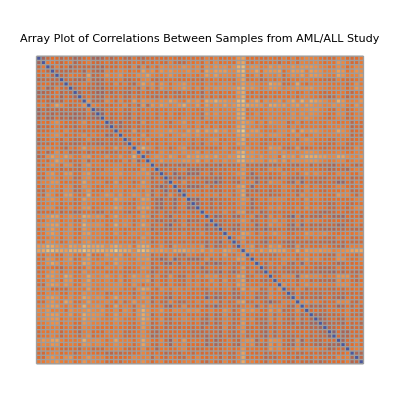

```mathematica
ArrayPlot[Correlation[dataGolubFull],
Mesh->True,
PlotTheme->"Scientific",PlotLabel->
"Array Plot of Correlations Between Samples 
from AML/ALL Study"]
```

```mathematica
<<MathIOmica`
```

MathIOmica (http://mathiomica.org), by [G. Mias Lab](http://georgemias.org).

```mathematica
clustersGolubCorrelation=MatrixClusters[Correlation[dataGolubFull],DistanceFunction->CorrelationDistance];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

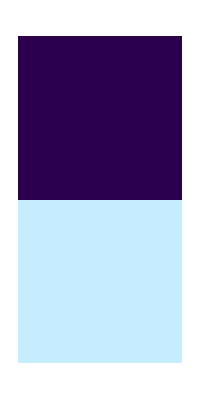
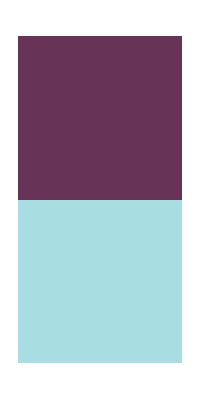
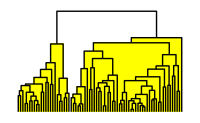
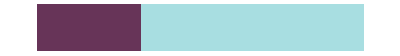
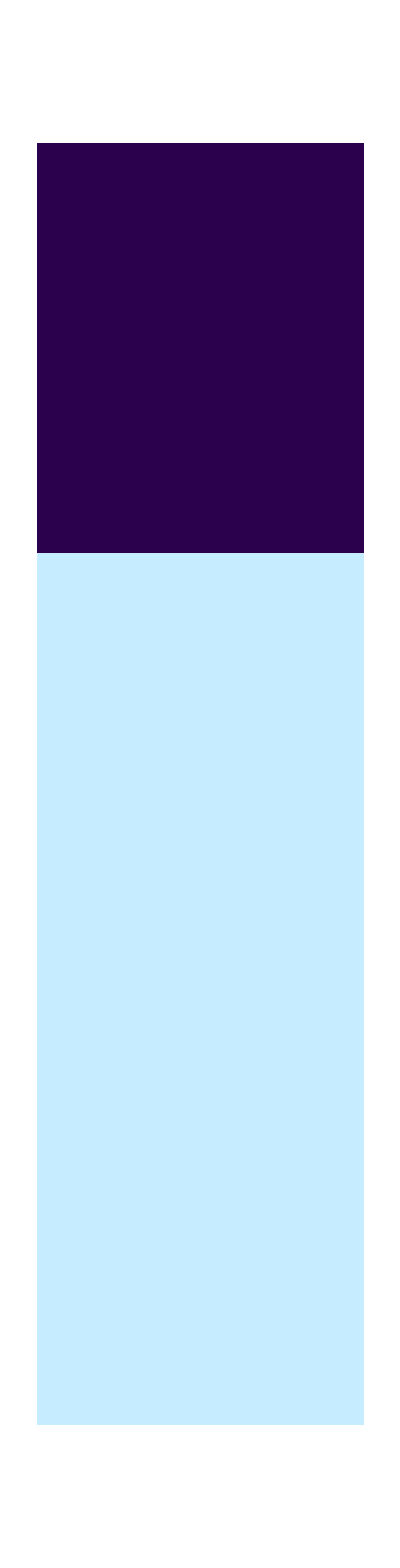
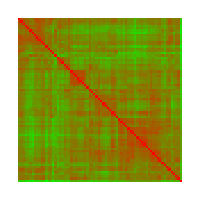
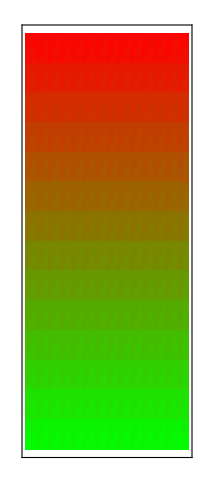
| 
Dendrogram and Heatmap | 
GroupAssociations | 
GroupIndex→Size | 
Rows | Columns
-Graphics- | -Graphics- |  | -Graphics- |  | 
 |  | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- |  | -Graphics-
 |  | -Graphics- |  | 
 |  | Groups |  |  |

```mathematica
MatrixDendrogramHeatmap[clustersGolubCorrelation[[1]],
ScaleShift-> 1]
```

```mathematica
Query[All,"GroupAssociationsRows"]@clustersGolubCorrelation
```

<|1→<|H:G1→{1,9,21,3,8,4,11,13,14,15,6,10,18,20,2,24,5,12,23,25,16,19,17},H:G2→{35,34,36,31,48,28,39,42,70,72,43,71,26,53,58,52,33,47,29,32,54,62,63,61,64,68,57,38,45,67,59,30,40,49,56,41,51,44,66,65,55,60,50,37,7,22,69,27,46}|>|>

```mathematica
?LinearModelFit
```

LinearModelFit[{y_1,y_2,…},{f_1,f_2,…},x] constructs a linear model of the form β_0+β_1 f_1+β_2 f_2+… that fits the y_i for successive x values 1, 2, ….
LinearModelFit[{{x_11,x_12,…,y_1},{x_21,x_22,…,y_2},…},{f_1,f_2,…},{x_1,x_2,…}] constructs a linear model of the form β_0+β_1 f_1+β_2 f_2+… where the f_i depend on the variables x_k. 
LinearModelFit[{m,v}] constructs a linear model from the design matrix m and response vector v.

```mathematica
modelGolub12=LinearModelFit[dataGolubFull[[All,1;;2]],x,x];
```

```mathematica
modelGolub12["Properties"]//Short
```

{AdjustedRSquared,AIC,«61»,VarianceInflationFactors}

```mathematica
modelGolub12["BestFit"]
```

1.11811×10^-15+0.831672 x

```mathematica
ToString[ modelGolub12@"RSquared"]
```

0.691679

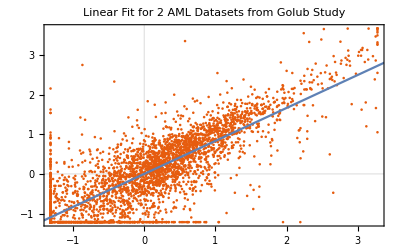

```mathematica
Show[ListPlot[dataGolubFull[[All,1;;2]],
PlotTheme-> "Scientific"],
Plot[modelGolub12["BestFit"],{x,-10,10},
PlotLegends->Grid[{{"Best Fit:",
Chop@modelGolub12["BestFit"]},
{"R^2:",ToString[ modelGolub12["RSquared"]]}}]],
PlotLabel-> 
"Linear Fit for 2 AML Datasets from Golub Study"]
```

### Moments of a distribution

```mathematica
data=N[RandomVariate[BinomialDistribution[100,0.1],50]]
```

{13.,9.,5.,8.,10.,12.,10.,2.,10.,6.,12.,10.,10.,11.,9.,15.,8.,13.,5.,12.,11.,8.,12.,6.,15.,9.,6.,7.,11.,10.,9.,13.,9.,10.,14.,7.,10.,6.,9.,7.,12.,15.,10.,7.,11.,8.,10.,11.,11.,10.}

```mathematica
CentralMoment[data,2]
```

7.4976

```mathematica
CentralMoment[data,4]
```

173.809

```mathematica
Skewness[data]
```

-0.230375

```mathematica
Kurtosis[data]
```

3.09192

```mathematica
CentralMoment[data,4]/CentralMoment[data,2]^2
```

3.09192

```mathematica
Table[CentralMoment[NormalDistribution[μ,σ],i],{i,6}]
```

{0,σ^2,0,3 σ^4,0,15 σ^6}

```mathematica
Table[CentralMoment[PoissonDistribution[μ],i],{i,6}]
```

{0,μ,μ,μ+3 μ^2,μ+10 μ^2,μ+25 μ^2+15 μ^3}

```mathematica
Kurtosis[NormalDistribution[μ,σ]]
```

3

```mathematica
TableForm[({ToString[#],Skewness[#],Kurtosis[#]}&/@{NormalDistribution[μ,σ],BinomialDistribution[n,p],ExponentialDistribution[λ],ChiSquareDistribution[ν],StudentTDistribution[ν]}),TableHeadings->{None,{"Distribution","Skewness","Kurtosis"}}]
```

Distribution | Skewness | Kurtosis
NormalDistribution[μ, σ] | 0 | 3
BinomialDistribution[n, p] | (1-2 p)/(√(n (1-p) p)) | 3+(1-6 (1-p) p)/(n (1-p) p)
ExponentialDistribution[λ] | 2 | 9
ChiSquareDistribution[ν] | 2 √2 √(1/ν) | 3+12/ν
StudentTDistribution[ν] | Piecewise[{{0, ν>3}, {Indeterminate, True}}] | Piecewise[{{3+6/(-4+ν), ν>4}, {Indeterminate, True}}]

### Distribution Fit

```mathematica
SeedRandom[123]
exponentialSampleData=RandomVariate[ExponentialDistribution[1],1000];
normalSampleData=RandomVariate[NormalDistribution[2,3],1000];
```

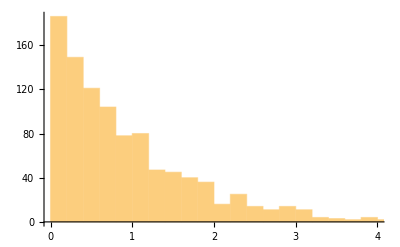
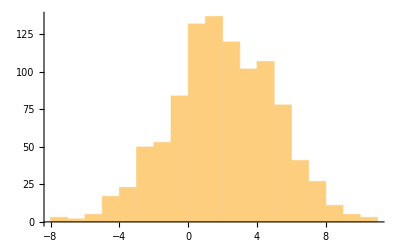

```mathematica
Histogram[#]&/@{exponentialSampleData,
normalSampleData}
```

```mathematica
DistributionFitTest[exponentialSampleData,NormalDistribution[2,3]]
```

1.33227×10^-15

```mathematica
DistributionFitTest[exponentialSampleData,ExponentialDistribution[1]]
```

0.489776

```mathematica
hFitExponentialSampleTests=DistributionFitTest[exponentialSampleData,NormalDistribution[2,3],"HypothesisTestData"];
```

```mathematica
hFitExponentialSampleTests["Properties"]
```

{AllTests,AndersonDarling,AutomaticTest,BaringhausHenze,CramerVonMises,DegreesOfFreedom,DistanceToBoundary,FittedDistribution,FittedDistributionParameters,HypothesisTestData,JarqueBeraALM,KolmogorovSmirnov,Kuiper,MardiaCombined,MardiaKurtosis,MardiaSkewness,PearsonChiSquare,Properties,PValue,PValueTable,ShapiroWilk,ShortTestConclusion,SzekelyEnergy,TestConclusion,TestData,TestDataTable,TestEntries,TestStatistic,TestStatisticTable,WatsonUSquare}

```mathematica
hFitExponentialSampleTests["TestDataTable",All]
```

| Statistic | P-Value
Anderson-Darling | 273.125 | 0.
Baringhaus-Henze | 327.828 | 0.
Cramér-von Mises | 57.0741 | 1.33227×10^-15
Jarque-Bera ALM | 1089.88 | 0.
Kolmogorov-Smirnov | 0.38977 | 3.26584×10^-133
Kuiper | 0.641303 | 3.0890777913417×10^-359
Mardia Combined | 1089.88 | 0.
Mardia Kurtosis | 24.6349 | 5.33911×10^-134
Mardia Skewness | 469.076 | 5.09234×10^-104
Pearson χ^2 | 3314.24 | 3.03067623786848×10^-685
Shapiro-Wilk | 0.847096 | 5.56647×10^-30
Watson U^2 | 38.8369 | 0.

```mathematica
hFitNormalSampleTests=DistributionFitTest[normalSampleData,NormalDistribution[2,3],"HypothesisTestData"];
```

```mathematica
hFitNormalSampleTests["TestDataTable",All]
```

| Statistic | P-Value
Anderson-Darling | 0.564789 | 0.681835
Baringhaus-Henze | 1.00766 | 0.204813
Cramér-von Mises | 0.0987282 | 0.591145
Jarque-Bera ALM | 2.14485 | 0.332788
Kolmogorov-Smirnov | 0.0224672 | 0.685025
Kuiper | 0.033845 | 0.667026
Mardia Combined | 2.14485 | 0.332788
Mardia Kurtosis | -0.497718 | 0.618683
Mardia Skewness | 1.91942 | 0.165921
Pearson χ^2 | 27.904 | 0.626117
Shapiro-Wilk | 0.998117 | 0.335309
Watson U^2 | 0.086213 | 0.362369

```mathematica
hFitExponentialSampleTests["TestConclusion"]
```

The null hypothesis that the data is distributed according to the NormalDistribution[2,3] is rejected at the 5 percent level based on the Cramér-von Mises test.

```mathematica
hFitNormalSampleTests["TestConclusion"]
```

The null hypothesis that the data is distributed according to the NormalDistribution[2,3] is not rejected at the 5 percent level based on the Cramér-von Mises test.

```mathematica
golubFirstSet=(Query["AML",All/*Values,1]@golubAssociation);
```

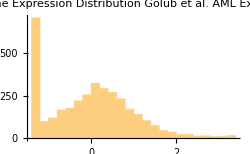

```mathematica
Histogram[golubFirstSet,
PlotLabel-> "Gene Expression Distribution
Golub et al. AML Example",
FrameLabel->{"Normalized Expression","Count"}]
```

```mathematica
hFitTestsGolubFirst=DistributionFitTest[golubFirstSet,NormalDistribution[],"HypothesisTestData"];
```

```mathematica
hFitTestsGolubFirst["TestDataTable",All]
```

| Statistic | P-Value
Anderson-Darling | 40.4247 | 0.
Baringhaus-Henze | 68.2693 | 0.
Cramér-von Mises | 3.83399 | 1.0965×10^-9
Jarque-Bera ALM | 154.672 | 0.
Mardia Combined | 154.672 | 0.
Mardia Kurtosis | 0.395616 | 0.692389
Mardia Skewness | 154.238 | 2.05421×10^-35
Pearson χ^2 | 6558.29 | 3.90378140987547×10^-1362
Shapiro-Wilk | 0.944707 | 1.20641×10^-34

```mathematica
hFitTestsGolubFirst["TestConclusion"]
```

The null hypothesis that the data is distributed according to the NormalDistribution[0,1] is rejected at the 5 percent level based on the Cramér-von Mises test.